```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["/Users/pwrzo/Documents/GitHub/Direct_Greens_Function/rotsaw/"],
SetDirectory["~/Documents/GitHub/Direct_Greens_Function/rotsaw/"]
]
```

/Users/pwrzosek/Documents/GitHub/Direct_Greens_Function/rotsaw

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/Users/pwrzosek/bin/pdflatex","Ghostscript"->"/usr/local/bin/gs"
]*)
<<MaTeX`;
```

```mathematica
fName={"FigBtNInew.png","FigSqNInew.png","FigSqnew.png"}
```

{FigBtNInew.png,FigSqNInew.png,FigSqnew.png}

```mathematica
figs=Table[Import[fig],{fig,fName}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
labels={MaTeX["\\textrm{(a)}",Magnification->1.5],MaTeX["\\textrm{(b)}",Magnification->1.5],MaTeX["\\textrm{(c)}",Magnification->1.5]};
titles={
MaTeX["\\textrm{Bethe~(no~m-m~int.)}",Magnification->1.5],
MaTeX["\\textrm{Square~(no~m-m~int.)}",Magnification->1.5],
MaTeX["\\textrm{Square~(with~m-m~int.)}",Magnification->1.5]
};
```

```mathematica
figsLabeled=Table[Show[figs[[it]],ImageSize->Medium,Epilog->{
Inset[labels[[it]],Scaled[{0.215, 0.86}]],
Inset[Graphics[{Opacity[0.05,Gray],Rectangle[{0,0},{1,0.1},RoundingRadius->0.05]}],Scaled[{0.5, 1.015}],{0.5,0},300]
},PlotLabel->titles[[it]]],{it,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
legend=Plot[{},{x,0,1},ImageSize->800,Frame->False,Axes->False,AspectRatio->1/6,
Epilog->{
Inset[MaTeX["x = P, D, F",Magnification->1.5],Scaled[{0.1,0.7}],{0,0}],
Inset[MaTeX["y = S, P, D, F",Magnification->1.5],Scaled[{0.25,0.7}],{0,0}],
Inset[MaTeX["l = 0",Magnification->1.5],Scaled[{0.52,0.7}],{0,0}],
Inset[MaTeX["l = 1",Magnification->1.5],Scaled[{0.72,0.7}],{0,0}],
Inset[MaTeX["l = 2",Magnification->1.5],Scaled[{0.92,0.7}],{0,0}],
Inset[grayMark,Scaled[{0.45,0.8}],{0,0},0.085],
Inset[redMark,Scaled[{0.65,0.8}],{0,0},0.085],
Inset[blueMark,Scaled[{0.85,0.8}],{0,0},0.085],
Inset[Graphics[{Opacity[0.1,Yellow],Rectangle[{0,0},{1,0.05},RoundingRadius->0.02]}],Scaled[{0.538, 0.67}],{0.5,0},0.97]
}
]
```

-Graphics-

```mathematica
(*AppendTo[figsLabeled,legend];*)
griD={Grid[{#},Dividers->{None,None},Alignment->{Left,Center},ItemSize->{Scaled[1/Length[#]],2}]}&;
```

```mathematica
fig1=Grid[griD/@{figsLabeled,{legend}},Spacings->{-4, 1}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics-

```mathematica
Export["Fig1n.png",fig1,ImageResolution->300]
```

Fig1n.png

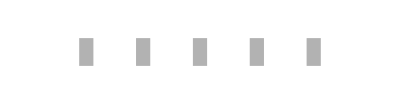

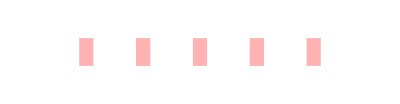

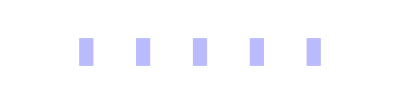

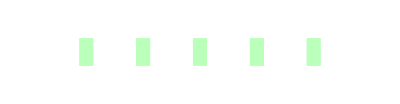

```mathematica
grayMark=Graphics[{
CapForm["Round"],Thickness[0.05],Opacity[0.9,Gray//Lighter],
Line[{{0,0},{0.05,0}}],
Line[{{0.2,0},{0.25,0}}],
Line[{{0.4,0},{0.45,0}}],
Line[{{0.6,0},{0.65,0}}],
Line[{{0.8,0},{0.85,0}}]
},
PlotRange->{{-0.15,1},{-0.15,0.15}}
]
redMark=Graphics[{
CapForm["Round"],Thickness[0.05],Opacity[0.9,Pink//Lighter],
Line[{{0,0},{0.05,0}}],
Line[{{0.2,0},{0.25,0}}],
Line[{{0.4,0},{0.45,0}}],
Line[{{0.6,0},{0.65,0}}],
Line[{{0.8,0},{0.85,0}}]
},
PlotRange->{{-0.15,1},{-0.15,0.15}}
]
blueMark=Graphics[{
CapForm["Round"],Thickness[0.05],Opacity[0.9,Blue//Lighter//Lighter//Lighter],
Line[{{0,0},{0.05,0}}],
Line[{{0.2,0},{0.25,0}}],
Line[{{0.4,0},{0.45,0}}],
Line[{{0.6,0},{0.65,0}}],
Line[{{0.8,0},{0.85,0}}]
},
PlotRange->{{-0.15,1},{-0.15,0.15}}
]
greenMark=Graphics[{
CapForm["Round"],Thickness[0.05],Opacity[0.9,Green//Lighter//Lighter//Lighter],
Line[{{0,0},{0.05,0}}],
Line[{{0.2,0},{0.25,0}}],
Line[{{0.4,0},{0.45,0}}],
Line[{{0.6,0},{0.65,0}}],
Line[{{0.8,0},{0.85,0}}]
},
PlotRange->{{-0.15,1},{-0.15,0.15}}
]
```